# De Sitter Greens Functions (d=3)

## Setup:

```mathematica
m:=0
h:=1.4
n:=7500
d:=3
l:=1
"causal events" n
"~ causal relations" n^2

A=CSDeSitterDGlobalSlabFull[h,d,n];
ρ:=CSize[A] / CVolume[A]
"density" ρ
Subscript[C, 1]=SparseArray[CausalMatrix[A]];

V=(IdentityMatrix[n]+Subscript[C, 1]).(IdentityMatrix[n]+Subscript[C, 1]);
Tau[Vol_?NumericQ]:=Piecewise[{{τ/. FindRoot[Vol==2 Pi (τ/2-Tanh[τ/2]),{τ,1}],Vol>0},{0,Vol==0}}]
(*
VolTime= Table[Tau[V[[i,j]]],{i,n},{j,n}];
VolTime=VolTime*Subscript[C, 1];
*)
K=Table[Piecewise[{{1/(2π Tau[V[[i,j]]]),V[[i,j]]>0},{0,V[[i,j]]==0}}],{i,n},{j,n}];
(*K=K0.Inverse[IdentityMatrix[n]+m^2/ρ K0];*)
(*
Subscript[C, 1]//MatrixForm
K //MatrixForm
A[[1,1]]
points=Transpose[{Flatten[VolTime],Flatten[K]}];
*)
```

7500 causal events

56250000 ~ causal relations

(density CSize[CSDeSitterDGlobalSlabFull[1.4,3,7500]])/CVolume[CSDeSitterDGlobalSlabFull[1.4,3,7500]]

SparseArray::list: List expected at position 1 in SparseArray[CausalMatrix[CSDeSitterDGlobalSlabFull[1.4,3,7500]]].

## Manifold Proper Time

```mathematica
MfdTime=Table[Re[ArcCosh[1/(Cos[A[[1,i,4]]]*Cos[A[[1,j,4]]])*(A[[1,i,1]]*A[[1,j,1]]+A[[1,i,2]]*A[[1,j,2]]+A[[1,i,3]]*A[[1,j,3]]-Sin[A[[1,i,4]]]*Sin[A[[1,j,4]]])]*Subscript[C, 1][[i,j]]],{i,n},{j,n}];
(*
MfdSpace=Im[ArcCosh[Z]];
MfdSpace= MfdSpace*(UpperTriangularize[ConstantArray[1,{n,n}],1]-Subscript[C, 1]);


time=Transpose[{Flatten[MfdTime],Flatten[N[K]]}];
time=DeleteCases[Chop[time],{0,_}];
Length[time]"No. of non-zero relations"
*)
```

## Whitman function for Causet :

```mathematica
iΔ=N[I*(K-Transpose[K])];
{EE,VV}=Chop[Eigensystem[iΔ]];
Q = Transpose[VV] . DiagonalMatrix[Clip[N[EE],{0, Max[N[Abs[EE]]]}]] . Conjugate[VV] // Chop;

pointsTime=Transpose[{Flatten[MfdTime],Flatten[Re[Q]]}];
pointsTime=DeleteCases[Chop[pointsTime],{0,_}];
(*pointsSpace=Transpose[{Flatten[MfdSpace],Flatten[Re[Q]]}];
*)
```

## Whitman function (Analytical):

```mathematica
Subscript[m, c]:=Sqrt[3]/2
M:= Sqrt[m^2+Subscript[m, c]^2]
d:=3
H1=(d-1)/2+Sqrt[((d-1)/2)^2-M^2 l^2];
H2=(d-1)/2-Sqrt[((d-1)/2)^2-M^2 l^2];
norm=Gamma[H1]*Gamma[H2]/((4*π)^(d/2)*l^2*Gamma[d/2]);
N[Re[norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1+Cosh[1])]]]
N[Limit[Re[norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1+Cosh[ϵ])]],{ϵ->0}]]
```

0.

0.

## Hadamard function (Re[W]):

-Graphics-

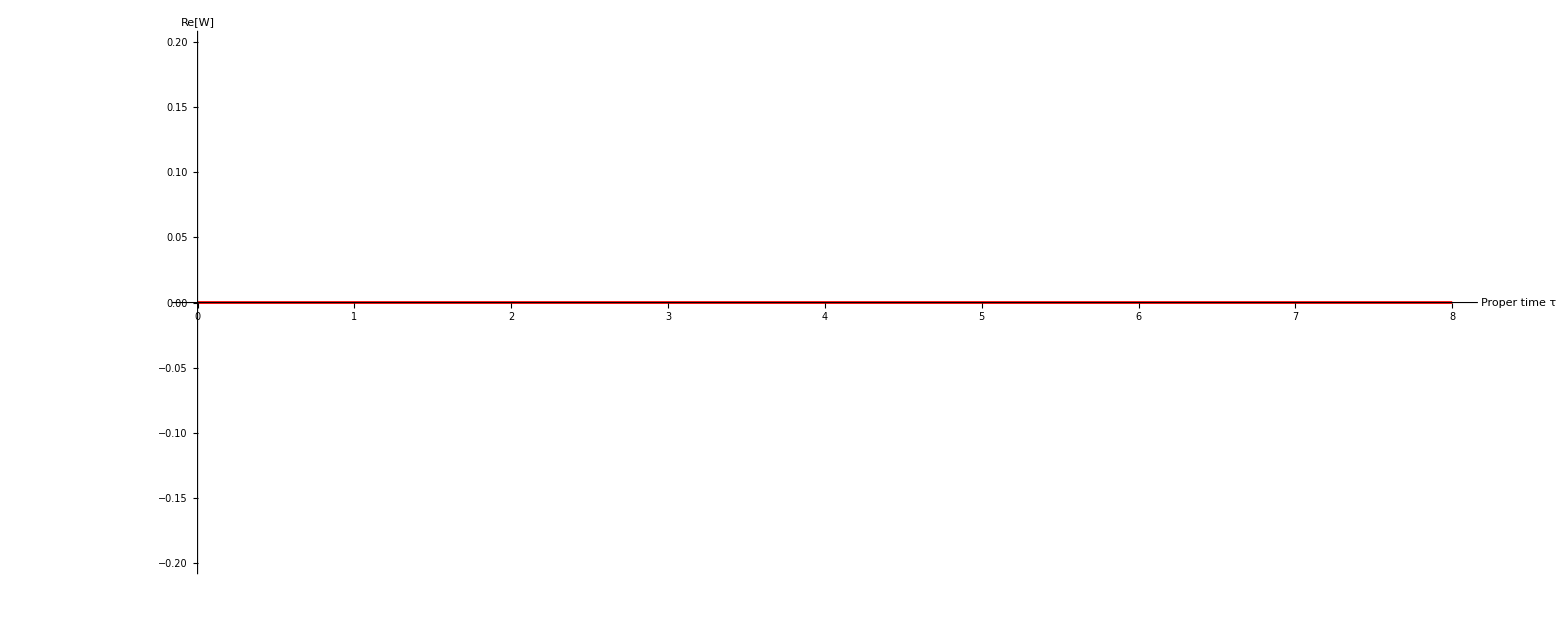

-Graphics-

```mathematica
sample:=400000
Show[ListPlot[RandomSample[pointsTime,sample],PlotStyle->PointSize[0.00001],ImageSize->600],Plot[Re[norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1+Cosh[τ])]],{τ,0,8},PlotStyle->Red,AspectRatio->Automatic,AxesLabel->{"Proper time τ","Re[W]"},PlotRange->{{0,8},{-.2,.2}}],PlotRange->{{0,8},{-.2,.2}}]
```

## Retarded Greens Functions:

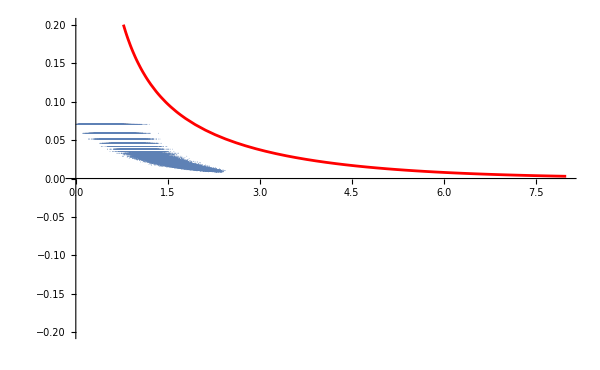

```mathematica
sample:=100000
Show[ListPlot[RandomSample[time,sample],PlotStyle->PointSize[0.00001],ImageSize->600],Plot[-2*norm*Im[Hypergeometric2F1[H1,H2,d/2,1/2*(1+Cosh[τ])]],{τ,0,8},PlotStyle->Red,AspectRatio->Automatic,AxesLabel->{"Proper time τ","Re[W]"},PlotRange->{{0,8},{-.2,.2}}],PlotRange->{{0,8},{-.2,.2}}]
```

## Space-like Separated points:

```mathematica
sample=10000;

plot5=ListPlot[pointsSpace,PlotStyle->PointSize[0.00001],ImageSize->600];
plot6=Plot[Re[norm*Hypergeometric2F1[H1,H2,d/2,1/2 *(1+Cos[τ])]],{τ,0,8},PlotStyle->Red,AspectRatio->Automatic,AxesLabel->{"Proper time τ","Re[W]"}];

Show[plot5,plot6,PlotRange-> {{0,8},{-.5,.5}}]
```

```mathematica
N[Limit[-2*Im[Hypergeometric2F1[H1,H2+ϵ,d/2,1/2*(1+Cosh[2])]]*Gamma[H1]*Gamma[H2+ϵ]/((4*π)^(d/2)*l^2*Gamma[d/2]),ϵ->0]]//FullSimplify (*This is a good way of taking hte massless limit that sems to work*)
```